```mathematica
Needs["PlotLegends`"]
```

```mathematica
R[q_,Γ_,E_,E0_]:=(q*Γ/2+E-E0)^2/((E-E0)^2 +(Γ/2)^2)
```

```mathematica
R1[q_,E_]:=R[q,2,E,0]
```

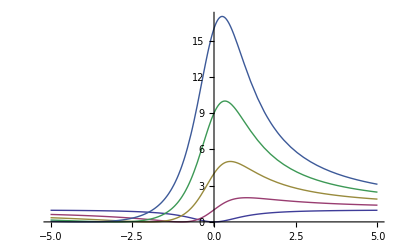

```mathematica
plt=Plot[{R1[0,x],R1[1,x],R1[2,x],R1[3,x],R1[4,x]},{x,-5,5},PlotLegend->{"q=0","q=1","q=2","q=3","q=4"},PlotRange->{All,All}]
```

```mathematica
Show[plt,Frame->True]
```

-Graphics-